```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues/Data/AccidentallyTiltingBoundaryConditionsBothInclusionsPositive/gpls/positive"];
ViewSurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
plot1=ListPlot3D[data,BoxRatios->Automatic];
plot2=ListPlot[Transpose[Drop[Transpose[data],-1]], PlotRange->{{ 0, 500}, {-500, 500}}];
{plot1,plot2}
]
files= FileNames[];
numbersInString[s_]:=ToExpression@StringCases[s,NumberString]
files = SortBy[files,numbersInString]
allPlots=Table[ViewSurface[file],{file,files}];
(*ListAnimate[allPlots]*)
```

{surface0positive.gpl,surface1positive.gpl,surface2positive.gpl,surface3positive.gpl,surface4positive.gpl,surface5positive.gpl,surface6positive.gpl,surface7positive.gpl,surface8positive.gpl,surface9positive.gpl,surface10positive.gpl,surface11positive.gpl,surface12positive.gpl,surface13positive.gpl,surface14positive.gpl,surface15positive.gpl,surface16positive.gpl,surface17positive.gpl,surface18positive.gpl,surface19positive.gpl,surface20positive.gpl,surface21positive.gpl,surface22positive.gpl,surface23positive.gpl,surface24positive.gpl,surface25positive.gpl,surface26positive.gpl,surface27positive.gpl,surface28positive.gpl,surface29positive.gpl,surface30positive.gpl,surface31positive.gpl,surface32positive.gpl,surface33positive.gpl,surface34positive.gpl,surface35positive.gpl,surface36positive.gpl,surface37positive.gpl,surface38positive.gpl,surface39positive.gpl,surface40positive.gpl,surface41positive.gpl,surface42positive.gpl,surface43positive.gpl,surface44positive.gpl,surface45positive.gpl,surface46positive.gpl,surface47positive.gpl,surface48positive.gpl,surface49positive.gpl,surface50positive.gpl,surface51positive.gpl,surface52positive.gpl,surface53positive.gpl,surface54positive.gpl,surface55positive.gpl,surface56positive.gpl,surface57positive.gpl,surface58positive.gpl,surface59positive.gpl,surface60positive.gpl,surface61positive.gpl,surface62positive.gpl,surface63positive.gpl,surface64positive.gpl,surface65positive.gpl,surface66positive.gpl,surface67positive.gpl,surface68positive.gpl,surface69positive.gpl,surface70positive.gpl,surface71positive.gpl,surface72positive.gpl,surface73positive.gpl,surface74positive.gpl,surface75positive.gpl,surface76positive.gpl,surface77positive.gpl,surface78positive.gpl,surface79positive.gpl,surface80positive.gpl,surface81positive.gpl,surface82positive.gpl,surface83positive.gpl,surface84positive.gpl,surface85positive.gpl,surface86positive.gpl,surface87positive.gpl,surface88positive.gpl,surface89positive.gpl,surface90positive.gpl,surface91positive.gpl,surface92positive.gpl,surface93positive.gpl,surface94positive.gpl,surface95positive.gpl,surface96positive.gpl,surface97positive.gpl,surface98positive.gpl,surface99positive.gpl,surface100positive.gpl,surface101positive.gpl,surface102positive.gpl,surface103positive.gpl,surface104positive.gpl,surface105positive.gpl,surface106positive.gpl,surface107positive.gpl,surface108positive.gpl,surface109positive.gpl,surface110positive.gpl,surface111positive.gpl,surface112positive.gpl,surface113positive.gpl,surface114positive.gpl,surface115positive.gpl,surface116positive.gpl,surface117positive.gpl,surface118positive.gpl,surface119positive.gpl,surface120positive.gpl,surface121positive.gpl,surface122positive.gpl,surface123positive.gpl,surface124positive.gpl,surface125positive.gpl,surface126positive.gpl,surface127positive.gpl,surface128positive.gpl,surface129positive.gpl,surface130positive.gpl,surface131positive.gpl,surface132positive.gpl,surface133positive.gpl,surface134positive.gpl,surface135positive.gpl,surface136positive.gpl,surface137positive.gpl,surface138positive.gpl,surface139positive.gpl,surface140positive.gpl,surface141positive.gpl,surface142positive.gpl,surface143positive.gpl,surface144positive.gpl,surface145positive.gpl,surface146positive.gpl,surface147positive.gpl,surface148positive.gpl,surface149positive.gpl,surface150positive.gpl,surface151positive.gpl,surface152positive.gpl,surface153positive.gpl,surface154positive.gpl,surface155positive.gpl,surface156positive.gpl,surface157positive.gpl,surface158positive.gpl,surface159positive.gpl,surface160positive.gpl,surface161positive.gpl,surface162positive.gpl,surface163positive.gpl,surface164positive.gpl,surface165positive.gpl,surface166positive.gpl,surface167positive.gpl,surface168positive.gpl,surface169positive.gpl,surface170positive.gpl}

{{50,5.55917×10^7},{60,5.55338×10^7},{70,5.50583×10^7},{80,5.35468×10^7},{90,5.27061×10^7},{100,5.18367×10^7},{110,5.10402×10^7},{120,5.02041×10^7},{130,4.81033×10^7},{140,4.74077×10^7},{150,4.67592×10^7},{160,4.62175×10^7},{170,4.55951×10^7},{180,4.50085×10^7},{190,4.44927×10^7},{200,4.40115×10^7},{210,4.38842×10^7},{220,4.36781×10^7},{230,4.35863×10^7},{240,4.28166×10^7},{250,4.24208×10^7},{260,4.20538×10^7},{270,4.24018×10^7},{280,4.20665×10^7},{290,4.17471×10^7},{300,4.14436×10^7},{310,4.08581×10^7},{320,3.91347×10^7},{330,4.14814×10^7},{340,3.85892×10^7},{350,3.8063×10^7},{360,3.76049×10^7},{370,3.62971×10^7},{380,3.60903×10^7},{390,3.56122×10^7},{400,3.53989×10^7},{410,3.50642×10^7},{420,3.45974×10^7},{430,3.42594×10^7},{440,3.31191×10^7},{450,3.29491×10^7},{460,3.27847×10^7},{470,3.26208×10^7},{480,3.24645×10^7},{490,3.16839×10^7},{500,3.14523×10^7},{510,3.13236×10^7},{520,3.09811×10^7},{530,3.08576×10^7},{540,3.07402×10^7},{550,2.9811×10^7},{560,2.96937×10^7},{570,2.9579×10^7},{580,2.94669×10^7},{590,2.9358×10^7},{600,2.92897×10^7},{610,2.91839×10^7},{620,2.91423×10^7},{630,2.90361×10^7},{640,2.88157×10^7},{650,2.87179×10^7},{660,2.86526×10^7},{670,2.85933×10^7},{680,2.81469×10^7},{690,2.80634×10^7},{700,2.79826×10^7},{710,2.78113×10^7},{720,2.77364×10^7},{730,2.76631×10^7},{740,2.7601×10^7},{750,2.66103×10^7},{760,2.65384×10^7},{770,2.62759×10^7},{780,2.62439×10^7},{790,2.61761×10^7},{800,2.6109×10^7},{810,2.5907×10^7},{820,2.58514×10^7},{830,2.57924×10^7},{840,2.57374×10^7},{850,2.56592×10^7},{860,2.55859×10^7},{870,2.55333×10^7},{880,2.54807×10^7},{890,2.54583×10^7},{900,2.54056×10^7},{910,2.53536×10^7},{920,2.53023×10^7},{930,2.52515×10^7},{940,2.52013×10^7},{950,2.51516×10^7},{960,2.51024×10^7},{970,2.50537×10^7},{980,2.50053×10^7},{990,2.49627×10^7},{1000,2.49155×10^7},{1010,2.48685×10^7},{1020,2.49176×10^7},{1030,2.48734×10^7},{1040,2.48293×10^7},{1050,2.47854×10^7},{1060,2.47417×10^7},{1070,2.46981×10^7},{1080,2.46546×10^7},{1090,2.46112×10^7},{1100,2.45677×10^7},{1110,2.45243×10^7},{1120,2.4457×10^7},{1130,2.4413×10^7},{1140,2.43648×10^7},{1150,2.43326×10^7},{1160,2.43086×10^7},{1170,2.42632×10^7},{1180,2.4218×10^7},{1190,2.41708×10^7},{1200,2.4266×10^7},{1210,2.42262×10^7},{1220,2.41846×10^7},{1230,2.415×10^7},{1240,2.45164×10^7},{1250,2.44795×10^7},{1260,2.53099×10^7},{1270,2.53008×10^7},{1280,2.52629×10^7},{1290,2.52244×10^7},{1300,2.53445×10^7},{1310,2.5307×10^7},{1320,2.52679×10^7},{1330,2.5602×10^7},{1340,2.55937×10^7},{1350,2.58918×10^7},{1360,2.5861×10^7},{1370,2.58597×10^7},{1380,2.58259×10^7},{1390,2.56198×10^7},{1400,2.55783×10^7},{1410,2.55471×10^7},{1420,2.55034×10^7},{1430,2.54572×10^7},{1440,2.54091×10^7},{1450,2.5359×10^7},{1460,2.62686×10^7},{1470,2.62127×10^7},{1480,2.61564×10^7},{1490,2.63733×10^7},{1500,2.63097×10^7},{1510,2.63463×10^7},{1520,2.63969×10^7},{1530,2.63197×10^7},{1540,2.62374×10^7},{1550,2.61523×10^7},{1560,2.6059×10^7},{1570,2.76009×10^7},{1580,2.82177×10^7},{1590,2.83383×10^7},{1600,2.81738×10^7},{1610,2.80791×10^7},{1620,2.72035×10^7},{1630,2.65278×10^7},{1640,2.81988×10^7},{1650,2.79951×10^7},{1660,2.8307×10^7},{1670,3.04904×10^7},{1680,2.79699×10^7},{1690,2.93798×10^7},{1700,2.83304×10^7},{1710,2.80746×10^7},{1720,2.78068×10^7},{1730,2.75251×10^7},{1740,2.66765×10^7},{1750,2.6361×10^7}}

{{50,555.917},{60,555.338},{70,550.583},{80,535.468},{90,527.061},{100,518.367},{110,510.402},{120,502.041},{130,481.033},{140,474.077},{150,467.592},{160,462.175},{170,455.951},{180,450.085},{190,444.927},{200,440.115},{210,438.842},{220,436.781},{230,435.863},{240,428.166},{250,424.208},{260,420.538},{270,424.018},{280,420.665},{290,417.471},{300,414.436},{310,408.581},{320,391.347},{330,414.814},{340,385.892},{350,380.63},{360,376.049},{370,362.971},{380,360.903},{390,356.122},{400,353.989},{410,350.642},{420,345.974},{430,342.594},{440,331.191},{450,329.491},{460,327.847},{470,326.208},{480,324.645},{490,316.839},{500,314.523},{510,313.236},{520,309.811},{530,308.576},{540,307.402},{550,298.11},{560,296.937},{570,295.79},{580,294.669},{590,293.58},{600,292.897},{610,291.839},{620,291.423},{630,290.361},{640,288.157},{650,287.179},{660,286.526},{670,285.933},{680,281.469},{690,280.634},{700,279.826},{710,278.113},{720,277.364},{730,276.631},{740,276.01},{750,266.103},{760,265.384},{770,262.759},{780,262.439},{790,261.761},{800,261.09},{810,259.07},{820,258.514},{830,257.924},{840,257.374},{850,256.592},{860,255.859},{870,255.333},{880,254.807},{890,254.583},{900,254.056},{910,253.536},{920,253.023},{930,252.515},{940,252.013},{950,251.516},{960,251.024},{970,250.537},{980,250.053},{990,249.627},{1000,249.155},{1010,248.685},{1020,249.176},{1030,248.734},{1040,248.293},{1050,247.854},{1060,247.417},{1070,246.981},{1080,246.546},{1090,246.112},{1100,245.677},{1110,245.243},{1120,244.57},{1130,244.13},{1140,243.648},{1150,243.326},{1160,243.086},{1170,242.632},{1180,242.18},{1190,241.708},{1200,242.66},{1210,242.262},{1220,241.846},{1230,241.5},{1240,245.164},{1250,244.795},{1260,253.099},{1270,253.008},{1280,252.629},{1290,252.244},{1300,253.445},{1310,253.07},{1320,252.679},{1330,256.02},{1340,255.937},{1350,258.918},{1360,258.61},{1370,258.597},{1380,258.259},{1390,256.198},{1400,255.783},{1410,255.471},{1420,255.034},{1430,254.572},{1440,254.091},{1450,253.59},{1460,262.686},{1470,262.127},{1480,261.564},{1490,263.733},{1500,263.097},{1510,263.463},{1520,263.969},{1530,263.197},{1540,262.374},{1550,261.523},{1560,260.59},{1570,276.009},{1580,282.177},{1590,283.383},{1600,281.738},{1610,280.791},{1620,272.035},{1630,265.278},{1640,281.988},{1650,279.951},{1660,283.07},{1670,304.904},{1680,279.699},{1690,293.798},{1700,283.304},{1710,280.746},{1720,278.068},{1730,275.251},{1740,266.765},{1750,263.61}}

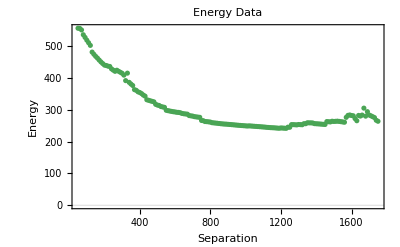

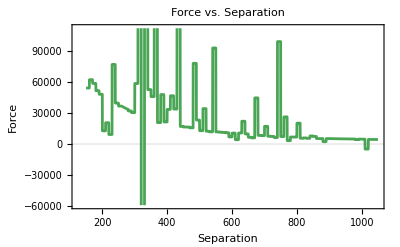

```mathematica
SolveForce[filename_] :=
Module[{stream, data,force, forcefunction, forceplot, x},
stream = OpenRead[filename];
data = ReadList[stream,{Number,Number}];
Close[stream];
data
];
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues"];
Print[SolveForce["energysep.txt"]];
allData=SolveForce["energysep.txt"];
{sep, energy}= Transpose[allData];
showData = Transpose[{sep,Map[#/(10^5)&,energy//N]}]
energyGraph = ListPlot[showData, PlotRange->All, PlotLabel->"Energy Data", PlotTheme->"Scientific", AxesLabel->{"Separation", "Energy"}, PlotStyle->Darker[Blend[{Green, LightBlue}]]]
(*ListPlot[allData,Joined->True]*)
force[x_]=-D[Interpolation[allData,InterpolationOrder->1][x],x];
forceGraph = Plot[force[x],{x,150, 1050},PlotTheme->"Scientific", AxesLabel->{"Separation", "Force"}, AxesOrigin->{125,-15}, PlotLabel->"Force vs. Separation", PlotStyle->{{Thickness[0.005],Darker[Blend[{Green, LightBlue}]]}}]
SetDirectory[StringJoin[NotebookDirectory[],"gpls/"]];
```

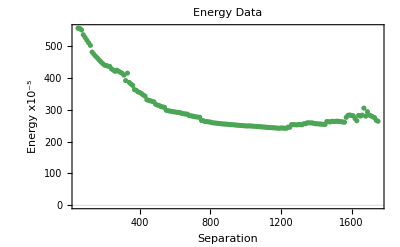

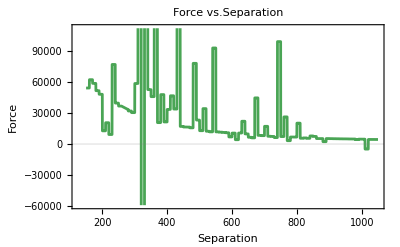

```mathematica
energyGraphnice = Show[energyGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Energy x10^("-5")],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Energy Data],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full]
forceGraphnice = Show[forceGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Force],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Force vs. Separation],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full]
```

```mathematica
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->20, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->{Automatic,Automatic,100}, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None];
prettyData
]
prettySurface["surface40positive.gpl"]
```

-Graphics3D-

```mathematica
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->10, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->Automatic, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None,PlotRange->{{-300,300},{-150,150},Automatic}];
Show[prettyData,Graphics3D[{Black,Sphere[{137.5,0,400},10],Cylinder[{{-137.5,0,399},{-137.5,0,401}},10]}]]
]
prettySurface["surface5positive.gpl"]
```

-Graphics3D-

```mathematica
|
```